## Mu vary

```mathematica
data=SemanticImport[NotebookDirectory[]<>"mu_0.0_1.0/output.csv"];
```

```mathematica
causes={"cbpp","rvf","age","health"};
```

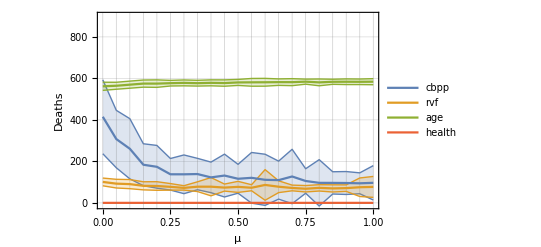

```mathematica
ListLinePlot[
(Transpose[
{Normal[data[[All,"ising_rvf_mu"]]],
Normal[Around[#[[1]],#[[2]]]&/@data[[All,{"d_"<>#<>"_mean","d_"<>#<>"_std"}]]]}])&/@causes,IntervalMarkers->"Bands",
PlotRange->{{0,1},{-10,900}},
PlotLegends->causes,
Frame->True,
FrameLabel->{"μ","Deaths"},
GridLines->{Table[i,{i,0,1,0.05}],Automatic}
]
```

```mathematica
Export[NotebookDirectory[]<>"mu-errorbars.png",%]
```

/Users/matt/wsu/livestock-agent-model/runs/spring_2020/mu-errorbars.png

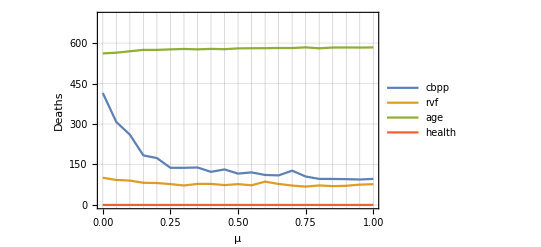

```mathematica
ListPlot[
Transpose[
{Normal[data[[All,"ising_rvf_mu"]]],
Normal[data[[All,"d_"<>#<>"_mean"]]]}]&/@causes,
Joined->True,
PlotRange->{{0,1},{0,700}},
PlotLegends->causes,
Frame->True,
FrameLabel->{"μ","Deaths"},
GridLines->{Table[i,{i,0,1,0.05}],Automatic}
]
```

```mathematica
Export[NotebookDirectory[]<>"mu-noerror.png",%]
```

/Users/matt/wsu/livestock-agent-model/runs/spring_2020/mu-noerror.png

## Date vary

```mathematica
data=SemanticImport[NotebookDirectory[]<>"vacc_date_newcbpp/output.csv"];
```

```mathematica
causes={"cbpp","rvf","age","health"};
```

```mathematica
causes={"cbpp","rvf"};
```

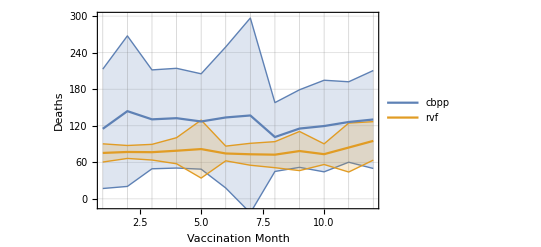

```mathematica
ListLinePlot[
(Transpose[
{Table[i,{i,1,12}],
Normal[Around[#[[1]],#[[2]]]&/@data[[All,{"d_"<>#<>"_mean","d_"<>#<>"_std"}]]]}])&/@causes,IntervalMarkers->"Bands",
PlotRange->{{1,12},{-10,300}},
PlotLegends->causes,
Frame->True,
FrameLabel->{"Vaccination Month","Deaths"},
GridLines->{Table[i,{i,1,12}],Automatic}
]
```

```mathematica
Export[NotebookDirectory[]<>"vaccdate-errorbars.png",%]
```

/Users/matt/wsu/livestock-agent-model/runs/spring_2020/vaccdate-errorbars.png

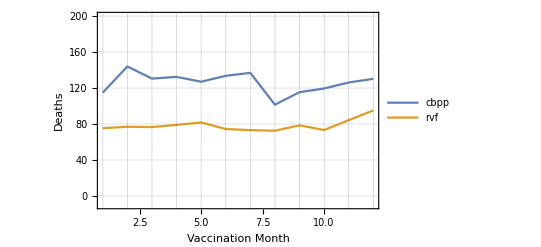

```mathematica
ListPlot[
Transpose[
{Table[i,{i,1,12}],
Normal[data[[All,"d_"<>#<>"_mean"]]]}]&/@causes,
Joined->True,
PlotRange->{{1,12},{-10,200}},
PlotLegends->causes,
Frame->True,
FrameLabel->{"Vaccination Month","Deaths"},
GridLines->{Table[i,{i,1,12}],Automatic}
]
```

```mathematica
Export[NotebookDirectory[]<>"vaccdate-noerror.png",%]
```

/Users/matt/wsu/livestock-agent-model/runs/spring_2020/vaccdate-noerror.png

```mathematica
data[[All,"d_rvf_mean"]]
```